```mathematica
(* Example Mathematica notebook code for Figure 7 in main text *)
(* Run using Mathematica version 12.0.0.0 on Mac OS X x86 (64-bit) *)
```

122.119

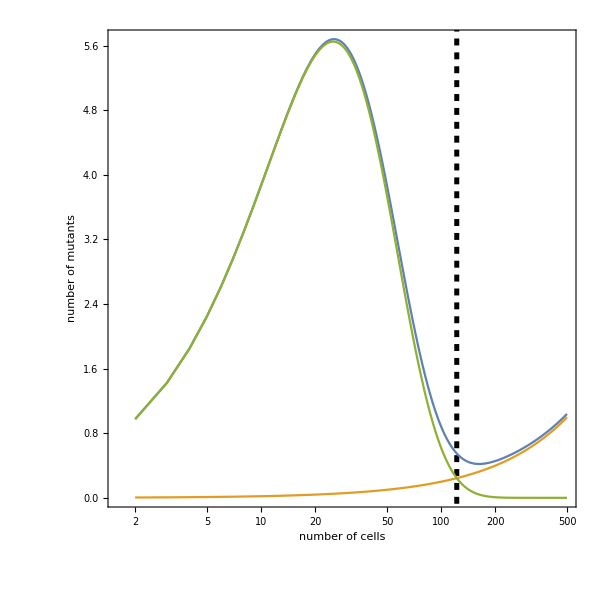

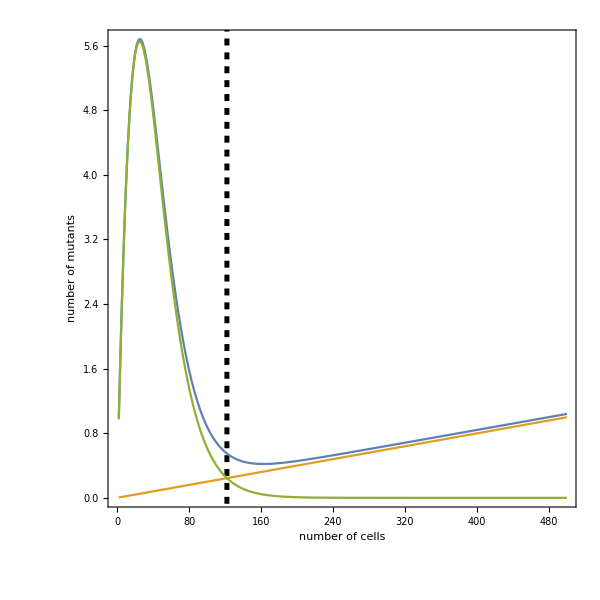

```mathematica
(* define parameters *)
mutationrate = 0.0001; mutationrateback = mutationrate; fitness= 0.95;

Npatch = 1;

listNcells = {};
Do[listNcells = AppendTo[listNcells,i],{i,2,500,1}];
listev = {};
listsm = {};
listapprox = {};
Ncells =.;

Do[Ncells=listNcells[[j]];
mat=Table[0,{x,Ncells+1},{y,Ncells+1}];
Do[Pdivm=((1-mutationrate)*fitness*(i-1) + mutationrate*(Ncells-(i-1)))/(fitness*(i-1)+Ncells-(i-1)) ; Pdiem=(i-1)/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem;
If[i>1,mat[[i,i-1]]=Pdown];
If[i<Ncells+1,mat[[i,i+1]]=Pup];
mat[[i,i]]=1-Pup-Pdown,{i,1,Ncells+1}]; 
mat = MatrixPower[mat,100000000]; (* simple way to determine the stationary distribution, can also use eigenvector of matrix associated with eigenvalue 1 *)

expectedvalue = 0;
Do[expectedvalue = expectedvalue + (i-1)*mat[[1,i]],{i,1,Ncells+1}];
smbalance = (Ncells*mutationrate/(1-fitness));
smbalance2 = Ncells/(2(1-fitness))*(1-fitness+mutationrate+fitness* mutationrate-Sqrt[(-1+mutationrate)^2+fitness^2 (-1+mutationrate)^2+2 fitness(-1+2 *mutationrate+mutationrate^2)]);
approxeq =(1- mutationrate/((fitness^(Ncells-1))*mutationrate+mutationrate))*Ncells;
listev = AppendTo[listev,expectedvalue*Npatch];
listsm = AppendTo[listsm,smbalance2*Npatch];
listapprox = AppendTo[listapprox,approxeq*Npatch];
,{j,1,Length[listNcells]}];

listplotev = {};
listplotsm = {};
listplotapprox ={};

Do[listplotev = AppendTo[listplotev,{listNcells[[i]],listev[[i]]}],{i,1,Length[listNcells]}]
Do[listplotsm = AppendTo[listplotsm,{listNcells[[i]],listsm[[i]]}],{i,1,Length[listNcells]}]
Do[listplotapprox = AppendTo[listplotapprox,{listNcells[[i]],listapprox[[i]]}],{i,1,Length[listNcells]}]

NC = Log[(((-1+fitness)*fitness)/(-1+fitness+mutationrate) - fitness*mutationrateback/mutationrate)]/Log[fitness]

thickness = 0.006;  

a = ListLogLinearPlot[{listplotev, listplotsm, listplotapprox},ImageSize->{600,600},Frame->True,FrameStyle->Bold,FrameLabel->{"number of cells","number of mutants"},PlotRange->All,AspectRatio-> Full,Joined->True,LabelStyle->{Bold,FontSize->36, FontColor->Black},PlotLabel->"",FrameTicksStyle->Directive[Black,36],Prolog->{Dashed,Thickness[thickness],Line[{{Log[NC],-10},{Log[NC],600}}]}]

b = ListPlot[{listplotev, listplotsm, listplotapprox},ImageSize->{600,600},Frame->True,FrameStyle->Bold,FrameLabel->{"number of cells","number of mutants"},PlotRange->All,AspectRatio-> Full,Joined->True,LabelStyle->{Bold,FontSize->36, FontColor->Black},PlotLabel->"",FrameTicksStyle->Directive[Black,36],Prolog->{Dashed,Thickness[thickness],Line[{{NC,-10},{NC,600}}]}]
```